# Spectral Problems for 2D Matrices

## Numerical Explorations

### Sampling

```mathematica
SeedRandom[906150257];(* from Poyla's conjecture for fun! *)
PoolSize=3000;
(* SPHERICAL MEASURES *)
HaarUnitaryPool=RandomVariate[CircularUnitaryMatrixDistribution[2],PoolSize];(* A large pool of Haar uniformly sampled 2x2 complex unitary matrices. *)
RandomUnitary:=RandomChoice[HaarUnitaryPool]

(* S MODIFIED MEASURES *)
HermitianAtCylindrical[ρ_,ϕ_,z_]:=ρ*Cos[ϕ]*PauliMatrix[1]+ρ*Sin[ϕ]*PauliMatrix[2]+z*PauliMatrix[3];

sDeformedPreFactor[s_,ξ_,z_]:=If[s==0,ξ,Sinh[2s*ξ]/(2s(Cosh[2s*ξ]-z Sinh[2s*ξ]))];

sDeformedDist[s_,ξ_]:=ProbabilityDistribution[sDeformedPreFactor[s,ξ,z],{z,-1,+1}]
Clear[sDeformedRandomOrbitElementPool];
(*sDeformedRandomOrbitElementPool[s_,ξ_,invert_:+1]:=sDeformedRandomOrbitElementPool[s,ξ,invert]=
Module[{randϕ,randz},
randϕ=RandomReal[{0,2*Pi},PoolSize];
(* Fix for Mathematicas buggy sampling for cocentrated measures on boundary ???? *)
randz=RandomVariate[sDeformedDist[s,ξ],PoolSize,Method->{"MCMC","Thinning"->10,"InitialVariance"->1,"InitialPoint"->0.01,"BurnInPeriod"->1000}];
Map[HermitianAtCylindrical[ξ*Sqrt[1-randz⟦#⟧^2],randϕ⟦#⟧,invert*ξ*randz⟦#⟧]&,Range[PoolSize]]
]*)
sDeformedRandomOrbitElementPool[s_,ξ_]:=sDeformedRandomOrbitElementPool[s,ξ]=
Module[{randϕ,randz},
randϕ=RandomReal[{0,2*Pi},PoolSize];
randz=RandomReal[{-ξ,ξ},PoolSize];
Map[{
{Exp[s*randz⟦#⟧],Exp[ⅈ*randϕ⟦#⟧]*Sqrt[Exp[2*s*ξ]+Exp[-2*s*ξ]-Exp[2*s*randz⟦#⟧]-Exp[-2*s*randz⟦#⟧]]},
{0,Exp[-s*randz⟦#⟧]}}&,
Range[PoolSize]]
]
```

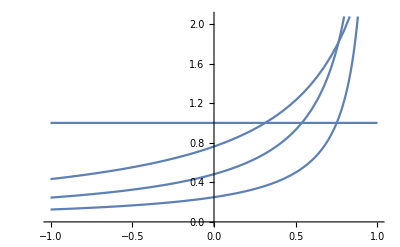

```mathematica
Plot[Map[sDeformedPreFactor[#,1,z]&,{0,0.5,1,2}],{z,-1,1},PlotRange->Automatic]
```

```mathematica
(* NOTE: Default randomvariate sampling is bad, MCMC handles things slightly better but is very sensitive to paramaters *)
```

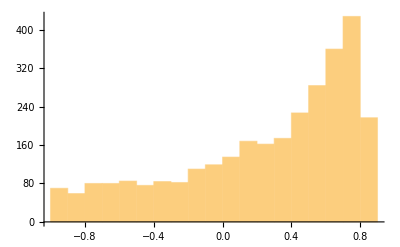
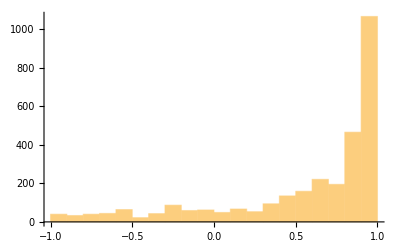

```mathematica
{Histogram[RandomVariate[sDeformedDist[1,1],PoolSize]],Histogram[RandomVariate[sDeformedDist[1,1],PoolSize,Method->{"MCMC","Thinning"->1,"InitialVariance"->1,"InitialPoint"->0.01,"BurnInPeriod"->100}]]}
```

```mathematica
ListPointPlot3D[Module[{randϕ,randz},
randϕ=RandomReal[{0,2*Pi},PoolSize];randz=RandomVariate[sDeformedDist[4,1],PoolSize,Method->{"MCMC","Thinning"->20,"InitialVariance"->0.01,"InitialPoint"->0.01,"BurnInPeriod"->1000}];
Map[{Sqrt[1-randz⟦#⟧^2]*Cos[randϕ⟦#⟧],Sqrt[1-randz⟦#⟧^2]*Sin[randϕ⟦#⟧],randz⟦#⟧}&,Range[PoolSize]]
],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

### Dealing with imprecision in imaginary parts

```mathematica
HermitianPart[matrix_]:=(matrix+ConjugateTranspose[matrix])/2;
RealEigenvalues[herm_]:=Map[Re,Eigenvalues[herm]];
RealSingularvalues[matrix_]:=Map[Re,SingularValueList[matrix]];
LeadingSingularvalue[matrix_]:=Max[Map[Re,SingularValueList[matrix]]];
```

### Anti-Transpose

```mathematica
AntiTranspose[M_]:=Transpose[Reverse[Transpose[Reverse[M]]]]
```

```mathematica
{MatrixForm[{{a,b},{c,d}}],MatrixForm[AntiTranspose[{{a,b},{c,d}}]]}
```

{(a | b
c | d),(d | c
b | a)}

### Orbit Parametrizations

```mathematica
CoadjointOrbit[λ_,U_]:=HermitianPart[U.DiagonalMatrix[λ].ConjugateTranspose[U]];

DressingOrbit[σ_,U_]  :=AntiTranspose[ConjugateTranspose[CholeskyDecomposition[AntiTranspose[CoadjointOrbit[σ^2,U]]]]]; 
(* Ensures singular values of DressingOrbit[σ,_] will be equal to σ *)

ReversedEMap=Function[{H},CholeskyDecomposition[HermitianPart[MatrixExp[2*H]]]];
(* Ensures ReversedEMap[CoadjointOrbit[λ,_]] equals DressingOrbit[σ,_] when σ^2 = e^(2λ)*)
(* Ensures singular values of ReversedEMap[H] are e^λ where λ are eigenvalues of H *)

EMap=Function[{H},AntiTranspose[ConjugateTranspose[CholeskyDecomposition[AntiTranspose[HermitianPart[MatrixExp[2*H]]]]]]];
(* Ensures EMap[CoadjointOrbit[λ,_]] equals DressingOrbit[σ,_] when σ^2 = e^(2λ)*)
(* Ensures singular values of EMap[H] are e^λ where λ are eigenvalues of H *)

GinzburgWeinstein[H_]:= (* taken from https://www.youtube.com/watch?v=U6MoHazD_YM *) (* See also "The U(n) Gelfand–Zeitlin system as a tropical limit of Ginzburg–Weinstein diffeomorphisms" *)
Module[{x,y,z,r,ϕ},
x=Tr[PauliMatrix[1].H]/2;
y=Tr[PauliMatrix[2].H]/2;
z=Tr[PauliMatrix[3].H]/2;
r=Sqrt[(x^2+y^2+z^2)];
ϕ=Arg[x+ⅈ*y];
{{Exp[z],Exp[ⅈ*ϕ]*Sqrt[Exp[2*r]-Exp[-2*r]-Exp[2*z]-Exp[-2*z]]},
{0,Exp[-z]}}]
```

### Sanity Checks with examples

#### Sanity check 1:

```mathematica
Module[{λ,U,H,D,GZH,EH,GZ},
λ={2,-1};
U=RandomUnitary;
H=CoadjointOrbit[λ,U];
EH=EMap[H];
D=DressingOrbit[Exp[λ],U];
GZ=GinzburgWeinstein[H];
TableForm[Transpose[
{{"Random Unitary",                                      MatrixForm[U]},
{"Hermitian with spectra λ",               MatrixForm[H]},
{"AMW EMap",                                                    MatrixForm[EH]},
{"Dressing orbit with singular e^λ",MatrixForm[D]},
{"GinzburgWeinstein[H]",                        MatrixForm[GZ]}
}]]
]
```

Random Unitary | Hermitian with spectra λ | AMW EMap | Dressing orbit with singular e^λ | GinzburgWeinstein[H]
(-0.142313-0.294515 ⅈ | -0.643183+0.692332 ⅈ
0.0614915+0.942988 ⅈ | -0.296334+0.138486 ⅈ) | (-0.679024+0. ⅈ | -0.859426+0.348268 ⅈ
-0.859426-0.348268 ⅈ | 1.67902+0. ⅈ) | (0.389236+0. ⅈ | -2.23412+0.905338 ⅈ
0.+0. ⅈ | 6.98363+0. ⅈ) | (0.389236+0. ⅈ | -2.23412+0.905338 ⅈ
0.+0. ⅈ | 6.98363+0. ⅈ) | (0.307579+0. ⅈ | -2.83709-1.14968 ⅈ
0 | 3.2512+0. ⅈ)

#### Sanity check 2:

```mathematica
Module[{λ1,λ2,U1,U2,H1,H2,E1,E2,E1a2,s},
s=0.01; (* small values of s correspond to linear limit *)
λ1={4,-1};                                 λ2={2,-3};
U1=RandomUnitary;                    U2=RandomUnitary;
H1=CoadjointOrbit[λ1,U1];H2=CoadjointOrbit[λ2,U2];
E1=EMap[s*H1];                         E2=EMap[s*H2];
E1a2=EMap[s*(H1+H2)];
TableForm[Join[{
{"λ[H1]","λ[H2]","λ[H1+H2]","σ[E[s*H1]]","σ[E[s*H2]]","σ[E[s*(H1+H2)]]","σ[E[s*H1].E[s*H2]]"},
{RealEigenvalues[H1],RealEigenvalues[H2],RealEigenvalues[H1+H2],RealSingularvalues[E1],RealSingularvalues[E2],RealSingularvalues[E1a2],RealSingularvalues[E1.E2]},
{"s^-1logσ[E[s*H1]]","s^-1logσ[E[s*H2]]","s^-1logσ[E[s*(H1+H2)]]","","","","s^-1logσ[E[s*H1].E[s*H2]]"},
{s^-1*Log[RealSingularvalues[E1]],s^-1*Log[RealSingularvalues[E2]],s^-1*Log[RealSingularvalues[E1a2]],"","","",s^-1*Log[RealSingularvalues[E1.E2]]}}
]]]
```

λ[H1] | λ[H2] | λ[H1+H2] | σ[E[s*H1]] | σ[E[s*H2]] | σ[E[s*(H1+H2)]] | σ[E[s*H1].E[s*H2]]
4.
-1. | -3.
2. | 5.20448
-3.20448 | 1.04081
0.99005 | 1.0202
0.970446 | 1.05342
0.968463 | 1.05358
0.968315
s^-1logσ[E[s*H1]] | s^-1logσ[E[s*H2]] | s^-1logσ[E[s*(H1+H2)]] |  |  |  | s^-1logσ[E[s*H1].E[s*H2]]
4.
-1. | 2.
-3. | 5.20448
-3.20448 |  |  |  | 5.21978
-3.21978

### Analytic Bounds on admissible regions

```mathematica
exampleα=N[11/10];exampleβ=N[1];exampleγ=N[4/5];
```

```mathematica
boundaryColor=RGBColor[0.2,0.7,0.0,0.1];
```

```mathematica
TracelessSpectraToAdmissibleRegion[a_,b_,c_]:=
Module[{xmin,xmax,ymin,ymax,t1,t2,t3},
xmin=Abs[b-a];
xmax=a+b;
ymin=Abs[c-b];
ymax=b+c;
t1=x^2+y^2-b^2;
t2=(-Sqrt[4 a^2 b^2-(a^2+b^2-x^2)^2]Sqrt[4 b^2 c^2-(b^2+c^2-y^2)^2])/(2 b^2);
t3=((a^2+b^2-x^2)(b^2+c^2-y^2))/(2 b^2);
Show[
Plot3D[Sqrt[t1+t2+t3],{x,xmin,xmax},{y,ymin,ymax},PlotStyle->boundaryColor,MeshStyle->Opacity[0.1],Axes->False,Boxed->False],
Plot3D[Sqrt[t1-t2+t3],{x,xmin,xmax},{y,ymin,ymax},PlotStyle->boundaryColor,MeshStyle->Opacity[0.1],Axes->False,Boxed->False]
]
]
```

```mathematica
TracelessSpectraToAdmissibleRegion[0.5,0.6,0.7]
```

-Graphics3D-

```mathematica
tripleAngleConstraint=Function[{Cosθab,Cosθbc,Cosθac},1≥Det[{{1,Cosθab,Cosθac},{Cosθab,1,Cosθbc},{Cosθac,Cosθbc,1}}]≥0];
(* Inequalities on angles from Gram matrix positivity
Minimize[{cosθac,tripleAngleConstraint[cosθab,cosθbc,cosθac]},cosθac]
Maximize[{cosθac,tripleAngleConstraint[cosθab,cosθbc,cosθac]},cosθac]
*)
```

```mathematica
TracelessSpectraToAdmissibleHyperbolicRegion[a_,b_,c_]:=
Function[{s},
Module[{xmin,xmax,ymin,ymax,halfFterm,Fdiffterm,cosθab,cosθbc,mincosθac,maxcosθac},

cosθab=(Cosh[2s*x]-Cosh[2s*a]Cosh[2s*b])/(Sinh[2s*a]Sinh[2s*b]);cosθbc=(Cosh[2s*y]-Cosh[2s*b]Cosh[2s*c])/(Sinh[2s*b]Sinh[2s*c]);
halfFterm=
Cosh[2 a s] Cosh[2 b s] Cosh[2 c s]+
Cosh[2s*c]Sinh[2s*b]Sinh[2s*a]cosθab+
Sinh[2s*c]Sinh[2s*b]Cosh[2s*a]cosθbc+
Sinh[2s*c]Cosh[2s*b]Sinh[2s*a]cosθab cosθbc+
-Sinh[2s*c]Sinh[2s*a]cosθab cosθbc;
Fdiffterm=Sinh[2s*a]Sinh[2s*c];
maxcosθac=cosθab cosθbc+√((-1+cosθab^2) (-1+cosθbc^2));
mincosθac=cosθab cosθbc-√((-1+cosθab^2) (-1+cosθbc^2));
xmin=Abs[b-a];
xmax=a+b;
ymin=Abs[c-b];
ymax=b+c;
Show[
Plot3D[ArcCosh[halfFterm+maxcosθac*Fdiffterm]/(2*s),{x,xmin,xmax},{y,ymin,ymax},PlotStyle->boundaryColor,MeshStyle->Opacity[0.1],Axes->False,Boxed->False],
Plot3D[ArcCosh[halfFterm+mincosθac*Fdiffterm]/(2*s),{x,xmin,xmax},{y,ymin,ymax},PlotStyle->boundaryColor,MeshStyle->Opacity[0.1],Axes->False,Boxed->False]
]
]
]
```

```mathematica
TracelessSpectraToAdmissibleHyperbolicRegion[exampleα,exampleβ,exampleγ][2]
```

-Graphics3D-

### Sampling admissible AB,BC,ABC regions

```mathematica
AdmissibleLeadingSingularValues=Function[{numSamples,α,β,γ},
Module[{UA,UB,UC,HA,HB,HC,EA,EB,EC,EAB,EBC,EABC,NormalLSAB,NormalLSBC,NormalLSABC,ExpFunction},
ExpFunction=MatrixExp;
(*
(* independent haar unitary samples *)
UA=HaarUnitaryPool⟦1;;numSamples⟧;
UB=HaarUnitaryPool⟦numSamples+1;;2*numSamples⟧;
UC=HaarUnitaryPool⟦2*numSamples+1;;3*numSamples⟧;
*)
(*
(* random coadjoint orbits with fixed spectra *)
HA=Map[CoadjointOrbit[{-α,α},#]&,UA];
HB=Map[CoadjointOrbit[{-β,β},#]&,UB];
HC=Map[CoadjointOrbit[{-γ,γ},#]&,UC];
*)
Function[{s},
(* independent s deformed random orbit samples *** traceless *** *)
EA=sDeformedRandomOrbitElementPool[s,α]⟦1;;numSamples⟧;
EB=sDeformedRandomOrbitElementPool[s,β]⟦1;;numSamples⟧;
EC=sDeformedRandomOrbitElementPool[s,γ]⟦1;;numSamples⟧;

(* random elements from orbits with fixed singular values (scaled by s) *)
(*
EA=Map[ExpFunction[s*HA⟦#⟧]&,Range[numSamples]];
EB=Map[ExpFunction[s*HB⟦#⟧]&,Range[numSamples]];
EC=Map[ExpFunction[s*HC⟦#⟧]&,Range[numSamples]];
*)
(* products of random dressed orbits *)
EAB=Map[EA⟦#⟧.EB⟦#⟧&,Range[numSamples]];
EBC=Map[EB⟦#⟧.EC⟦#⟧&,Range[numSamples]];
EABC=Map[EA⟦#⟧.EB⟦#⟧.EC⟦#⟧&,Range[numSamples]];
(* normalized leading singular values of these products *)
NormalLSAB=Map[s^-1*Log[LeadingSingularvalue[#]]&,EAB];
NormalLSBC=Map[s^-1*Log[LeadingSingularvalue[#]]&,EBC];
NormalLSABC=Map[s^-1*Log[LeadingSingularvalue[#]]&,EABC];
(* Plotting leading singular values *)
{s,Transpose[{NormalLSAB,NormalLSBC,NormalLSABC}]}
]
]];
ALSVOutputToPlot[data_,options_]:=
Module[{sString},sString=ToString[NumberForm[N[IntegerPart[N[100*data⟦1⟧]]/100],{4,2}]];
ListPointPlot3D[data⟦2⟧,
AxesLabel->{Style["σ(AB)",Medium],Style["σ(BC)",Medium],Style["σ(ABC)",Medium]},
BoxRatios->1,
PlotLabel->Style[StringReplace["s=sVal","sVal"->sString],Large],
ImageSize->Large,
PlotStyle->{PointSize[0.005],Opacity->1},
options]
]
```

```mathematica
(* EXAMPLE *) 
ALSVOutputToPlot[AdmissibleLeadingSingularValues[PoolSize,exampleα,exampleβ,exampleγ][0.004],{}]
```

-Graphics3D-

```mathematica
(* TRACELESS *)
Manipulate[Show[
ALSVOutputToPlot[AdmissibleLeadingSingularValues[PoolSize,α,β,γ][s],{}],
TracelessSpectraToAdmissibleHyperbolicRegion[α,β,γ][s]
,PlotRange->All],
{{α,+1.1},0.0,+2},
{{β,+1},0.0,+2},
{{γ,+0.8},0.0,+2},
{{s,0.000001},0.000001,8},
ContentSize->{1000, 800}(*,TrackedSymbols:>{α,β,γ,s}*)]
```

Show::gcomb: Could not combine the graphics objects in 
    Show[ALSVOutputToPlot[AdmissibleLeadingSingularValues[PoolSize, 1.1, 1, 
        0.8][7.34], {}], TracelessSpectraToAdmissibleHyperbolicRegion[1.1, 1, 
       0.8][7.34], PlotRange -> All].

### Animating the s parameter

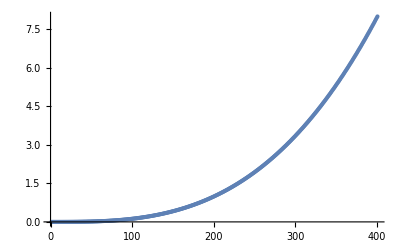

```mathematica
sValues=Map[8*#^3&,Range[0.00001,1.00001,1/400]];
numSValues=Length[sValues];
ListPlot[sValues]
```

```mathematica
preComputedSPlots1=Map[
AdmissibleLeadingSingularValues[PoolSize,exampleα,exampleβ,exampleγ]
,sValues];
```

```mathematica
plotRange[a_,b_,c_]:={{Abs[b-a],a+b},{Abs[c-b],b+c},{0,a+b+c}}
smallSViewPoint={0.0*Pi,-0.5*Pi,0.0};
largeSViewPoint={0.5*Pi,-0.65*Pi,-0.3};
```

```mathematica
(* For visualizing the animation *)
(*Manipulate[
Grid[
{
{Show[
ALSVOutputToPlot[preComputedSPlots1⟦i⟧,{}],
TracelessSpectraToAdmissibleHyperbolicRegion[exampleα,exampleβ,exampleγ][sValues⟦i⟧]
,PlotRange->plotRange[exampleα,exampleβ,exampleγ]
],
Show[
ALSVOutputToPlot[preComputedSPlots1⟦i⟧,ViewPoint->smallSViewPoint],
TracelessSpectraToAdmissibleHyperbolicRegion[exampleα,exampleβ,exampleγ][sValues⟦i⟧]
,PlotRange->plotRange[exampleα,exampleβ,exampleγ]
],
Show[
ALSVOutputToPlot[preComputedSPlots1⟦i⟧,ViewPoint->largeSViewPoint],
TracelessSpectraToAdmissibleHyperbolicRegion[exampleα,exampleβ,exampleγ][sValues⟦i⟧]
,PlotRange->plotRange[exampleα,exampleβ,exampleγ]
]
}
}
],
{i,1,numSValues,1},ContentSize->{1800, 800}
]*)
```

### Exploring Animations

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\cygwin64\home\TC\projects\admissible-orbits\code

```mathematica
animationData=Map[
Grid[
{
{
Show[
ALSVOutputToPlot[preComputedSPlots1⟦#⟧,{}],
TracelessSpectraToAdmissibleHyperbolicRegion[exampleα,exampleβ,exampleγ][sValues⟦#⟧]
,PlotRange->plotRange[exampleα,exampleβ,exampleγ]
],
Show[
ALSVOutputToPlot[preComputedSPlots1⟦#⟧,ViewPoint->smallSViewPoint],
TracelessSpectraToAdmissibleHyperbolicRegion[exampleα,exampleβ,exampleγ][sValues⟦#⟧]
,PlotRange->plotRange[exampleα,exampleβ,exampleγ]
],
Show[
ALSVOutputToPlot[preComputedSPlots1⟦#⟧,ViewPoint->largeSViewPoint],
TracelessSpectraToAdmissibleHyperbolicRegion[exampleα,exampleβ,exampleγ][sValues⟦#⟧]
,PlotRange->plotRange[exampleα,exampleβ,exampleγ]
]
}
}
]
&,
Range[1,numSValues,1]
];
```

```mathematica
Export["Singular values ABC, AB, and BC increasing s for (a_b_c)=(1.1_1.0_0.8) 1000 samples cubic interp correct measure.gif",animationData]
```

Singular values ABC, AB, and BC increasing s for (a_b_c)=(1.1_1.0_0.8) 1000 samples cubic interp correct measure.gif

## Entropy Inequalities

#### Binary Entropy

```mathematica
h[x_]:=If[x==0||x==1,0,If[0≤x≤1,-x Log[x]-(1-x)Log[1-x],Assert[False]]]
```

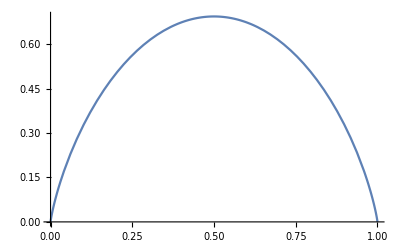

```mathematica
Plot[h[x],{x,0,1}]
```

### Strong Subadditivity & Weak Monotonicity

```mathematica
SSANonUniformIneq[μ_,a_,b_,c_,x_,y_,z_]:=(h[(2(a+b))/μ]+(2(a+b))/μ*h[1/2+x/(2(a+b))])+(h[(2(b+c))/μ]+(2(b+c))/μ*h[1/2+y/(2(b+c))])-(h[(2(b))/μ]+(2(b))/μ*h[1/2+b/(2(b))])-(h[(2(a+b+c))/μ]+(2(a+b+c))/μ*h[1/2+z/(2(a+b+c))]);
SSANonUniformIneqFullyGeneral[λ_,t_,u_,v_,a_,b_,c_,x_,y_,z_]:=(h[λ(t+u)]+λ(t+u)*h[1/2+x/(t+u)])+(h[λ(u+v)]+λ(u+v)*h[1/2+y/(u+v)])-(h[λ(u)]+λ(u)*h[1/2+b/(u)])-(h[λ(t+u+v)]+λ(t+u+v)*h[1/2+z/(t+u+v)]);
```

```mathematica
SSANonUniformIneqFullyGeneral[λ_,2a+t,2b+u,2c+v,a,b,c,x,y,z]
```

```mathematica
LargeMuSurplus[x_,y_,z_]:=y*Log[(y*(x+y+z))/((x+y)*(y+z))]-x*Log[(x+y)/(x+y+z)]-z*Log[(y+z)/(x+y+z)];
SSANonUniformIneqLargeMu[a_,b_,c_,x_,y_,z_]:=(2(a+b)*h[1/2+x/(2(a+b))])+(2(b+c)*h[1/2+y/(2(b+c))])-(2(b)*h[1/2+b/(2(b))])-(2(a+b+c)*h[1/2+z/(2(a+b+c))])+LargeMuSurplus[2a,2b,2c];
```

```mathematica
WMNonUniformIneq[μ_,a_,b_,c_,x_,y_,z_]:=(h[(2(a+b))/μ]+(2(a+b))/μ*h[1/2+x/(2(a+b))])+(h[(2(b+c))/μ]+(2(b+c))/μ*h[1/2+y/(2(b+c))])-(h[(2(c))/μ]+(2(c))/μ*h[1/2+c/(2(c))])-(h[(2(a))/μ]+(2(a))/μ*h[1/2+a/(2(a))]);
```

```mathematica
SSANonUniformIneqLargeMu[exampleα,exampleβ,exampleγ,exampleα+exampleβ,exampleβ+exampleγ,exampleα+exampleβ+exampleγ]
```

0.943153

```mathematica
(* Take μ increasing !!! *)
Grid[{Map[
Show[
RegionPlot3D[SSANonUniformIneq[z+3*(exampleα+exampleβ+exampleγ)+#,exampleα,exampleβ,exampleγ,x,y,z]<0,
{x,Abs[exampleα-exampleβ],exampleα+exampleβ},{y,Abs[exampleγ-exampleβ],exampleγ+exampleβ},{z,0,exampleα+exampleβ+exampleγ}
],
TracelessSpectraToAdmissibleRegion[exampleα,exampleβ,exampleγ]
]&,
{0,5,20,100}
]}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
(* SSA with maximum Mu *)
Show[
RegionPlot3D[(SSANonUniformIneqLargeMu[exampleα,exampleβ,exampleγ,x,y,z]<0),
{x,Abs[exampleα-exampleβ],exampleα+exampleβ},{y,Abs[exampleγ-exampleβ],exampleγ+exampleβ},{z,0,exampleα+exampleβ+exampleγ}
],
TracelessSpectraToAdmissibleRegion[exampleα,exampleβ,exampleγ]
]
```

-Graphics3D-

```mathematica
(* ALL Triangle inequalities *)
triangleIneqs[a_,b_,c_]:=(Abs[y-a]≤z≤y+a)&&(Abs[x-c]≤z≤x+c)&&(Abs[b-a]≤x≤b+a)&&(Abs[z-c]≤x≤z+c)&&(Abs[b-c]≤y≤b+c)&&(Abs[z-a]≤y≤z+a)
Show[
RegionPlot3D[Not[triangleIneqs[exampleα,exampleβ,exampleγ]],
{x,Abs[exampleα-exampleβ],exampleα+exampleβ},{y,Abs[exampleγ-exampleβ],exampleγ+exampleβ},{z,0,exampleα+exampleβ+exampleγ}
,PlotPoints->30],
TracelessSpectraToAdmissibleRegion[exampleα,exampleβ,exampleγ]
]
```

-Graphics3D-

```mathematica
(* Unrealizability witnessed by SSA but not face triangle inequalities *)
Show[
RegionPlot3D[(SSANonUniformIneqLargeMu[exampleα,exampleβ,exampleγ,x,y,z]<0)&&triangleIneqs[exampleα,exampleβ,exampleγ],
{x,Abs[exampleα-exampleβ],exampleα+exampleβ},{y,Abs[exampleγ-exampleβ],exampleγ+exampleβ},{z,0,exampleα+exampleβ+exampleγ}
],
TracelessSpectraToAdmissibleRegion[exampleα,exampleβ,exampleγ]
]
```

-Graphics3D-

```mathematica
(* QUALITATIVE CONCLUSION: most discriminating option is minimimal shifting and maximal scaling! *)
Show[
RegionPlot3D[(SSANonUniformIneqFullyGeneral[0.001,2exampleα,2exampleβ+1,2exampleγ+1,exampleα,exampleβ,exampleγ,x,y,z]<0),
{x,Abs[exampleα-exampleβ],exampleα+exampleβ},{y,Abs[exampleγ-exampleβ],exampleγ+exampleβ},{z,0,exampleα+exampleβ+exampleγ}
],
TracelessSpectraToAdmissibleRegion[exampleα,exampleβ,exampleγ]
]
```

-Graphics3D-

```mathematica
Show[
DensityPlot3D[SSANonUniformIneqLargeMu[exampleα,exampleβ,exampleγ,x,y,z],
{x,Abs[exampleα-exampleβ],exampleα+exampleβ},{y,Abs[exampleγ-exampleβ],exampleγ+exampleβ},{z,0,exampleα+exampleβ+exampleγ}
],
TracelessSpectraToAdmissibleRegion[exampleα,exampleβ,exampleγ]
]
```

-Graphics3D-

## Analytics

```mathematica
t1=x^2+y^2-b^2;
t2=(-Sqrt[4 a^2 b^2-(a^2+b^2-x^2)^2]Sqrt[4 b^2 c^2-(b^2+c^2-y^2)^2])/(2 b^2);
t3=((a^2+b^2-x^2)(b^2+c^2-y^2))/(2 b^2);
Expand[2 b^2*(t1+t3)]
```

a^2 b^2-b^4+a^2 c^2+b^2 c^2+b^2 x^2-c^2 x^2-a^2 y^2+b^2 y^2+x^2 y^2

```mathematica
jacobian={
D[Sqrt[a^2+b^2-2a*b*Cos[ϕ]],{{ϕ,ψ,η}}],
D[Sqrt[b^2+c^2-2b*c*Cos[ψ]],{{ϕ,ψ,η}}],
D[Sqrt[a^2+b^2+c^2-2b*c*Cos[ψ]-2a*b*Cos[ϕ]-2a*c*(Cos[η]Sin[ϕ]Sin[ψ]-Cos[ϕ]Cos[ψ])],{{ϕ,ψ,η}}]
};MatrixForm[jacobian]
```

((a b Sin[ϕ])/(√(a^2+b^2-2 a b Cos[ϕ])) | 0 | 0
0 | (b c Sin[ψ])/(√(b^2+c^2-2 b c Cos[ψ])) | 0
(2 a b Sin[ϕ]-2 a c (Cos[ψ] Sin[ϕ]+Cos[η] Cos[ϕ] Sin[ψ]))/(2 √(a^2+b^2+c^2-2 a b Cos[ϕ]-2 b c Cos[ψ]-2 a c (-Cos[ϕ] Cos[ψ]+Cos[η] Sin[ϕ] Sin[ψ]))) | (2 b c Sin[ψ]-2 a c (Cos[η] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ]))/(2 √(a^2+b^2+c^2-2 a b Cos[ϕ]-2 b c Cos[ψ]-2 a c (-Cos[ϕ] Cos[ψ]+Cos[η] Sin[ϕ] Sin[ψ]))) | (a c Sin[η] Sin[ϕ] Sin[ψ])/(√(a^2+b^2+c^2-2 a b Cos[ϕ]-2 b c Cos[ψ]-2 a c (-Cos[ϕ] Cos[ψ]+Cos[η] Sin[ϕ] Sin[ψ]))))

```mathematica
Simplify[Det[jacobian]]
```

(a^2 b^2 c^2 Sin[η] Sin[ϕ]^2 Sin[ψ]^2)/(√(a^2+b^2-2 a b Cos[ϕ]) √(b^2+c^2-2 b c Cos[ψ]) √(a^2+b^2+c^2-2 b c Cos[ψ]-2 a Cos[ϕ] (b-c Cos[ψ])-2 a c Cos[η] Sin[ϕ] Sin[ψ]))

```mathematica
Cη=(x^2+y^2-b^2+((a^2+b^2-x^2)(c^2+b^2-y^2))/(2 b^2)-z^2)((2 b^2)/(Sqrt[4 a^2 b^2-(a^2+b^2-x^2)^2]Sqrt[4 b^2 c^2-(b^2+c^2-y^2)^2]))
```

(2 b^2 (-b^2+x^2+y^2+((a^2+b^2-x^2) (b^2+c^2-y^2))/(2 b^2)-z^2))/(√(4 a^2 b^2-(a^2+b^2-x^2)^2) √(4 b^2 c^2-(b^2+c^2-y^2)^2))

```mathematica
Sϕ=Sqrt[1-((a^2+b^2-x^2)^2)/(4 a^2 b^2)]
```

√(1-((a^2+b^2-x^2)^2)/(4 a^2 b^2))

```mathematica
Sψ=Sqrt[1-((b^2+c^2-y^2)^2)/(4 b^2 c^2)]
```

√(1-((b^2+c^2-y^2)^2)/(4 b^2 c^2))

```mathematica
Simplify[(Sqrt[1-Cη^2]*Sϕ*Sψ)^2]
```

-(a^4 c^2+b^4 z^2+x^2 (y^2 (x^2+y^2-z^2)+c^2 (-y^2+z^2))-b^2 (z^2 (y^2-z^2)+c^2 (-y^2+z^2)+x^2 (y^2+z^2))-a^2 (-c^4+y^2 (x^2-z^2)+b^2 (c^2-x^2+z^2)+c^2 (x^2+y^2+z^2)))/(4 a^2 b^2 c^2)

```mathematica
Q[a_,b_,c_,x_,y_,z_]:=Expand[-(a^4 c^2+b^4 z^2+x^2 (y^2 (x^2+y^2-z^2)+c^2 (-y^2+z^2))-b^2 (z^2 (y^2-z^2)+c^2 (-y^2+z^2)+x^2 (y^2+z^2))-a^2 (-c^4+y^2 (x^2-z^2)+b^2 (c^2-x^2+z^2)+c^2 (x^2+y^2+z^2)))]
```

```mathematica
Q[a,b,c,x,y,z]
```

-a^4 c^2+a^2 b^2 c^2-a^2 c^4-a^2 b^2 x^2+a^2 c^2 x^2+a^2 c^2 y^2-b^2 c^2 y^2+a^2 x^2 y^2+b^2 x^2 y^2+c^2 x^2 y^2-x^4 y^2-x^2 y^4+a^2 b^2 z^2-b^4 z^2+a^2 c^2 z^2+b^2 c^2 z^2+b^2 x^2 z^2-c^2 x^2 z^2-a^2 y^2 z^2+b^2 y^2 z^2+x^2 y^2 z^2-b^2 z^4

```mathematica
VolTetraSquared[a_,b_,c_,x_,y_,z_]:=Det[{{2 a^2,a^2+b^2-z^2,c^2+a^2-y^2},{a^2+b^2-z^2,2 b^2,b^2+c^2-x^2},{c^2+a^2-y^2,b^2+c^2-x^2,2 c^2}}]/288
```

```mathematica
Permutations[{a,b,c,x,y,z}]⟦Position[Map[Simplify[(144*Apply[VolTetraSquared,#]-Q[a,b,c,x,y,z])]&,Permutations[{a,b,c,x,y,z}]],0]⟦2⟧⟧
```

{{a,x,z,c,y,b}}

```mathematica
RelabeledVolTetraSquared[a_,b_,c_,x_,y_,z_]:=
VolTetraSquared[a,x,z,c,y,b]
```

```mathematica
Expand[144*RelabeledVolTetraSquared[a,b,c,x,y,z]]-Q[a,b,c,x,y,z]
```

0

```mathematica
-Q[a,b,c,x,y,z]
```

a^2 b^2 x^2-b^2 c^2 x^2-a^2 b^2 y^2+b^2 c^2 y^2-a^2 x^2 z^2+c^2 x^2 z^2+a^2 y^2 z^2-c^2 y^2 z^2

```mathematica
FullSimplify[((2a*b*c)/Sqrt[Q[a,b,c,x,y,z]])^2-(1/(Sqrt[1-Cη^2]*Sϕ*Sψ))^2]
```

0

```mathematica
Prob[a_,b_,c_]:=Function[{x,y,z},
Module[{xmin,xmax,ymin,ymax,t1,t2,t3},
xmin=Abs[b-a];
xmax=a+b;
ymin=Abs[c-b];
ymax=b+c;

t1=x^2+y^2-b^2;
t2=(-Sqrt[4 a^2 b^2-(a^2+b^2-x^2)^2]Sqrt[4 b^2 c^2-(b^2+c^2-y^2)^2])/(2 b^2);
t3=((a^2+b^2-x^2)(b^2+c^2-y^2))/(2 b^2);
If[(xmin<=x<=xmax)&&(ymin<=y<=ymax)&&
Im[t2]<=10^-4&&Im[t1-t2+t3]<=10^-4&&Re[t1-t2+t3]>=0&&
(Sqrt[Re[t1+t2+t3]]<=z<=Sqrt[Re[t1-t2+t3]]),
(x*y*z)/(2*Pi*a*b*c*Sqrt[Q[a,b,c,x,y,z]]),0]
]];
```

```mathematica
Prob[0.5,0.6,0.7][1.1,0.1,0.4]
```

6.32963×10^6

```mathematica
Plot3D[Prob[0.5,0.6,0.7][0.3,y,z],{y,0,1},{z,0,1}]
```

-Graphics3D-

```mathematica
DensityPlot3DWithTetrahedraDensity[a_,b_,c_]:=
Module[{xmin,xmax,ymin,ymax,t1,t2,t3},
xmin=Abs[b-a];
xmax=a+b;
ymin=Abs[c-b];
ymax=b+c;
DensityPlot3D[Min[Prob[a,b,c][x,y,z],5],
{x,xmin,xmax},{y,ymin,ymax},{z,0,a+b+c},
AxesLabel->Automatic,PlotPoints->50]
]
```

```mathematica
DensityPlot3DWithTetrahedraDensity[exampleα,exampleβ,exampleγ]
```

-Graphics3D-

### Hyperbolic Analytics

```mathematica
hyperbolicAdmissibilityCondition=
(Cosh[2s*z] Sinh[2s*b]^2-
Cosh[2 a s] Cosh[2 b s] Cosh[2 c s] Sinh[2s*b]^2-
Cosh[2s*c] Sinh[2s*b]^2(Cosh[2s*x]-Cosh[2s*a]Cosh[2s*b])-
Cosh[2s*a] Sinh[2s*b]^2(Cosh[2s*y]-Cosh[2s*b]Cosh[2s*c])-
Cosh[2s*b](Cosh[2s*x]-Cosh[2s*a]Cosh[2s*b]) (Cosh[2s*y]-Cosh[2s*b]Cosh[2s*c]))^2<=(Sinh[2s*c]Sinh[2s*a] Sinh[2s*b]^2)^2(-1+((Cosh[2s*x]-Cosh[2s*a]Cosh[2s*b])/(Sinh[2s*a]Sinh[2s*b]))^2) (-1+((Cosh[2s*y]-Cosh[2s*b]Cosh[2s*c])/(Sinh[2s*b]Sinh[2s*c]))^2);
```

```mathematica
hyperbolicAdmissibilityConditionPositiveForm2=Simplify[TrigExpand[(-(Sinh[2s*a]Sinh[2s*b])^2+(Cosh[2s*x]-Cosh[2s*a]Cosh[2s*b])^2) (-(Sinh[2s*b]Sinh[2s*c])^2+(Cosh[2s*y]-Cosh[2s*b]Cosh[2s*c])^2)-(Cosh[2s*z] Sinh[2s*b]^2-
Cosh[2 a s] Cosh[2 b s] Cosh[2 c s] Sinh[2s*b]^2-
Cosh[2s*c] Sinh[2s*b]^2(Cosh[2s*x]-Cosh[2s*a]Cosh[2s*b])-
Cosh[2s*a] Sinh[2s*b]^2(Cosh[2s*y]-Cosh[2s*b]Cosh[2s*c])-
Cosh[2s*b](Cosh[2s*x]-Cosh[2s*a]Cosh[2s*b]) (Cosh[2s*y]-Cosh[2s*b]Cosh[2s*c]))^2]]
```

-1/8 (-10-2 Cosh[4 a s]-2 Cosh[4 b s]+Cosh[4 (a-c) s]-2 Cosh[4 c s]+Cosh[4 (a+c) s]+4 Cosh[2 s (a-b-x)]+4 Cosh[2 s (a+b-x)]-2 Cosh[4 s x]+4 Cosh[2 s (a-b+x)]+4 Cosh[2 s (a+b+x)]+4 Cosh[2 s (b-c-y)]+4 Cosh[2 s (b+c-y)]-2 Cosh[2 s (a-c-x-y)]-2 Cosh[2 s (a+c-x-y)]+Cosh[4 s (x-y)]-2 Cosh[2 s (a-c+x-y)]-2 Cosh[2 s (a+c+x-y)]-2 Cosh[4 s y]+4 Cosh[2 s (b-c+y)]+4 Cosh[2 s (b+c+y)]-2 Cosh[2 s (a-c-x+y)]-2 Cosh[2 s (a+c-x+y)]+Cosh[4 s (x+y)]-2 Cosh[2 s (a-c+x+y)]-2 Cosh[2 s (a+c+x+y)]+Cosh[4 s (b-z)]-2 Cosh[2 s (a-b-c-z)]-2 Cosh[2 s (a+b-c-z)]-2 Cosh[2 s (a-b+c-z)]-2 Cosh[2 s (a+b+c-z)]+4 Cosh[2 s (c-x-z)]+4 Cosh[2 s (c+x-z)]+4 Cosh[2 s (a-y-z)]-2 Cosh[2 s (b-x-y-z)]-2 Cosh[2 s (b+x-y-z)]+4 Cosh[2 s (a+y-z)]-2 Cosh[2 s (b-x+y-z)]-2 Cosh[2 s (b+x+y-z)]-2 Cosh[4 s z]+Cosh[4 s (b+z)]-2 Cosh[2 s (a-b-c+z)]-2 Cosh[2 s (a+b-c+z)]-2 Cosh[2 s (a-b+c+z)]-2 Cosh[2 s (a+b+c+z)]+4 Cosh[2 s (c-x+z)]+4 Cosh[2 s (c+x+z)]+4 Cosh[2 s (a-y+z)]-2 Cosh[2 s (b-x-y+z)]-2 Cosh[2 s (b+x-y+z)]+4 Cosh[2 s (a+y+z)]-2 Cosh[2 s (b-x+y+z)]-2 Cosh[2 s (b+x+y+z)]) Sinh[2 b s]^2

```mathematica
hyperbolicAdmissibilityConditionPositiveForm3=-(-10-2 Cosh[4 a s]-2 Cosh[4 b s]+Cosh[4 (a-c) s]-2 Cosh[4 c s]+Cosh[4 (a+c) s]+4 Cosh[2 s (a-b-x)]+4 Cosh[2 s (a+b-x)]-2 Cosh[4 s x]+4 Cosh[2 s (a-b+x)]+4 Cosh[2 s (a+b+x)]+4 Cosh[2 s (b-c-y)]+4 Cosh[2 s (b+c-y)]-2 Cosh[2 s (a-c-x-y)]-2 Cosh[2 s (a+c-x-y)]+Cosh[4 s (x-y)]-2 Cosh[2 s (a-c+x-y)]-2 Cosh[2 s (a+c+x-y)]-2 Cosh[4 s y]+4 Cosh[2 s (b-c+y)]+4 Cosh[2 s (b+c+y)]-2 Cosh[2 s (a-c-x+y)]-2 Cosh[2 s (a+c-x+y)]+Cosh[4 s (x+y)]-2 Cosh[2 s (a-c+x+y)]-2 Cosh[2 s (a+c+x+y)]+Cosh[4 s (b-z)]-2 Cosh[2 s (a-b-c-z)]-2 Cosh[2 s (a+b-c-z)]-2 Cosh[2 s (a-b+c-z)]-2 Cosh[2 s (a+b+c-z)]+4 Cosh[2 s (c-x-z)]+4 Cosh[2 s (c+x-z)]+4 Cosh[2 s (a-y-z)]-2 Cosh[2 s (b-x-y-z)]-2 Cosh[2 s (b+x-y-z)]+4 Cosh[2 s (a+y-z)]-2 Cosh[2 s (b-x+y-z)]-2 Cosh[2 s (b+x+y-z)]-2 Cosh[4 s z]+Cosh[4 s (b+z)]-2 Cosh[2 s (a-b-c+z)]-2 Cosh[2 s (a+b-c+z)]-2 Cosh[2 s (a-b+c+z)]-2 Cosh[2 s (a+b+c+z)]+4 Cosh[2 s (c-x+z)]+4 Cosh[2 s (c+x+z)]+4 Cosh[2 s (a-y+z)]-2 Cosh[2 s (b-x-y+z)]-2 Cosh[2 s (b+x-y+z)]+4 Cosh[2 s (a+y+z)]-2 Cosh[2 s (b-x+y+z)]-2 Cosh[2 s (b+x+y+z)])
```

10+2 Cosh[4 a s]+2 Cosh[4 b s]-Cosh[4 (a-c) s]+2 Cosh[4 c s]-Cosh[4 (a+c) s]-4 Cosh[2 s (a-b-x)]-4 Cosh[2 s (a+b-x)]+2 Cosh[4 s x]-4 Cosh[2 s (a-b+x)]-4 Cosh[2 s (a+b+x)]-4 Cosh[2 s (b-c-y)]-4 Cosh[2 s (b+c-y)]+2 Cosh[2 s (a-c-x-y)]+2 Cosh[2 s (a+c-x-y)]-Cosh[4 s (x-y)]+2 Cosh[2 s (a-c+x-y)]+2 Cosh[2 s (a+c+x-y)]+2 Cosh[4 s y]-4 Cosh[2 s (b-c+y)]-4 Cosh[2 s (b+c+y)]+2 Cosh[2 s (a-c-x+y)]+2 Cosh[2 s (a+c-x+y)]-Cosh[4 s (x+y)]+2 Cosh[2 s (a-c+x+y)]+2 Cosh[2 s (a+c+x+y)]-Cosh[4 s (b-z)]+2 Cosh[2 s (a-b-c-z)]+2 Cosh[2 s (a+b-c-z)]+2 Cosh[2 s (a-b+c-z)]+2 Cosh[2 s (a+b+c-z)]-4 Cosh[2 s (c-x-z)]-4 Cosh[2 s (c+x-z)]-4 Cosh[2 s (a-y-z)]+2 Cosh[2 s (b-x-y-z)]+2 Cosh[2 s (b+x-y-z)]-4 Cosh[2 s (a+y-z)]+2 Cosh[2 s (b-x+y-z)]+2 Cosh[2 s (b+x+y-z)]+2 Cosh[4 s z]-Cosh[4 s (b+z)]+2 Cosh[2 s (a-b-c+z)]+2 Cosh[2 s (a+b-c+z)]+2 Cosh[2 s (a-b+c+z)]+2 Cosh[2 s (a+b+c+z)]-4 Cosh[2 s (c-x+z)]-4 Cosh[2 s (c+x+z)]-4 Cosh[2 s (a-y+z)]+2 Cosh[2 s (b-x-y+z)]+2 Cosh[2 s (b+x-y+z)]-4 Cosh[2 s (a+y+z)]+2 Cosh[2 s (b-x+y+z)]+2 Cosh[2 s (b+x+y+z)]

```mathematica
hyperbolicAdmissibilityConditionPositiveForm3PosCoeffTerms=10+2 Cosh[4 a s]+2 Cosh[4 b s]+2 Cosh[4 c s]+2 Cosh[4 s x]+2 Cosh[2 s (a-c-x-y)]+2 Cosh[2 s (a+c-x-y)]+2 Cosh[2 s (a-c+x-y)]+2 Cosh[2 s (a+c+x-y)]+2 Cosh[4 s y]+2 Cosh[2 s (a-c-x+y)]+2 Cosh[2 s (a+c-x+y)]+2 Cosh[2 s (a-c+x+y)]+2 Cosh[2 s (a+c+x+y)]+2 Cosh[2 s (a-b-c-z)]+2 Cosh[2 s (a+b-c-z)]+2 Cosh[2 s (a-b+c-z)]+2 Cosh[2 s (a+b+c-z)]+2 Cosh[2 s (b-x-y-z)]+2 Cosh[2 s (b+x-y-z)]+2 Cosh[2 s (b-x+y-z)]+2 Cosh[2 s (b+x+y-z)]+2 Cosh[4 s z]+2 Cosh[2 s (a-b-c+z)]+2 Cosh[2 s (a+b-c+z)]+2 Cosh[2 s (a-b+c+z)]+2 Cosh[2 s (a+b+c+z)]+2 Cosh[2 s (b-x-y+z)]+2 Cosh[2 s (b+x-y+z)]+2 Cosh[2 s (b-x+y+z)]+2 Cosh[2 s (b+x+y+z)];hyperbolicAdmissibilityConditionPositiveForm3NegTerms=hyperbolicAdmissibilityConditionPositiveForm3-hyperbolicAdmissibilityConditionPositiveForm3PosCoeffTerms;
```

```mathematica
hyperbolicAdmissibilityConditionPositiveForm3NegTerms*-1
```

Cosh[4 (a-c) s]+Cosh[4 (a+c) s]+4 Cosh[2 s (a-b-x)]+4 Cosh[2 s (a+b-x)]+4 Cosh[2 s (a-b+x)]+4 Cosh[2 s (a+b+x)]+4 Cosh[2 s (b-c-y)]+4 Cosh[2 s (b+c-y)]+Cosh[4 s (x-y)]+4 Cosh[2 s (b-c+y)]+4 Cosh[2 s (b+c+y)]+Cosh[4 s (x+y)]+Cosh[4 s (b-z)]+4 Cosh[2 s (c-x-z)]+4 Cosh[2 s (c+x-z)]+4 Cosh[2 s (a-y-z)]+4 Cosh[2 s (a+y-z)]+Cosh[4 s (b+z)]+4 Cosh[2 s (c-x+z)]+4 Cosh[2 s (c+x+z)]+4 Cosh[2 s (a-y+z)]+4 Cosh[2 s (a+y+z)]

```mathematica
hyperbolicAdmissibilityConditionPositiveForm3PosCoeffTermsLargestCandidates={(a+b+c+z),(b+x+y+z),(a+c+x+y)};
hyperbolicAdmissibilityConditionPositiveForm3NegCoeffTermsLargestCandidates={ (a+y+z), (c+x+z),(b+z),(x+y),(b+c+y),(a+b+x),2*(a+c)};
```

```mathematica
Simplify[Max[hyperbolicAdmissibilityConditionPositiveForm3PosCoeffTermsLargestCandidates]≥Max[hyperbolicAdmissibilityConditionPositiveForm3NegCoeffTermsLargestCandidates]]
```

Max[a+c+x+y,a+b+c+z,b+x+y+z]≥Max[2 (a+c),a+b+x,b+c+y,x+y,b+z,c+x+z,a+y+z]

```mathematica
Show[
RegionPlot3D[(hyperbolicAdmissibilityConditionPositiveForm3≥0/.{a->exampleα,b->exampleβ,c->exampleγ,s->0.8}),
{x,Abs[exampleα-exampleβ],exampleα+exampleβ},{y,Abs[exampleγ-exampleβ],exampleγ+exampleβ},{z,0,exampleα+exampleβ+exampleγ}
],
TracelessSpectraToAdmissibleRegion[exampleα,exampleβ,exampleγ]
]
```

-Graphics3D-

```mathematica
Limit[s^-1 Log[Exp[s*a]+Exp[s*b]+Exp[s*c]],s->Infinity]
```

ConditionalExpression[c, a>0&&a<b&&b>0&&a<c&&b<c&&c>0]